```mathematica
Monitor[ParallelTable[
With[
{fileName="d:\\Saved\\Exports\\5\\"<>ToString[k]<>".png"},
If[!FileExistsQ[fileName],
PrintTemporary[k];
Export[fileName,SummaryPrintGood5[k],ImageResolution->200]
]
],{k,Sort[Keys[allGraphs5]]}];,k]
```

```mathematica
..
```

```mathematica
SummaryPrintGood4[k_]:=Block[
{g=MobiusGraphDoubleGood[K4Key,k,allGraphs4], gr=allGraphs4[k,"graph"],compKey=FindComplement[k,allGraphs4],comp={},g2},
comp=allGraphs4[compKey,"graph"];
g2=MobiusGraphDoubleGood[K4Key,compKey,allGraphs4];
Framed[
Labeled[
Column[{
TableForm[{Labeled[Graph[gr,ImageSize->150],Style[k,Bold,12, Underlined,Red]],Labeled[Graph[comp,ImageSize->150],Style[compKey,Bold,12, Underlined,Red]]}, TableDirections->Row],
Graph[g,ImageSize->800],
Graph[g2,ImageSize->800]
},Alignment->Center],
{Style[StandardForm[allGraphs4[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Row[Table[Style[ChromaticPolynomial[gr,m],Blue],{m,1,4}], " * "],
Framed[Style[StandardForm[((allGraphs4[k,"colofour"]/.rep4))],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

```mathematica
Monitor[ParallelTable[
With[
{fileName="d:\\Saved\\Exports\\4\\"<>ToString[k]<>".png"},
If[!FileExistsQ[fileName],
PrintTemporary[k];
Export[fileName,SummaryPrintGood4[k],ImageResolution->200]
]
],{k,Sort[Keys[allGraphs4]]}];,k]
```

0

16

40

90

18

45

91

1

49

22

93

2

54

26

94

3

27

63

97

4

28

72

108

6

81

30

109

9

82

31

110

10

84

36

111

12

85

37

112

13

87

39

117

14

118

218

270

309

120

243

271

324

121

244

273

325

122

245

274

327

136

246

276

328

145

247

279

333

162

252

280

334

165

253

282

336

168

255

283

337

190

256

286

193

342

257

300

346

364

417

546

351

365

442

352

367

445

576

353

369

448

577

354

373

473

606

355

377

486

607

382

357

487

608

391

360

488

400

361

637

414

516

363

517

666

697

728

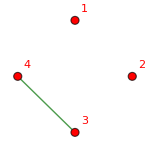
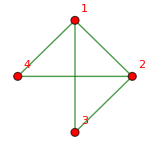
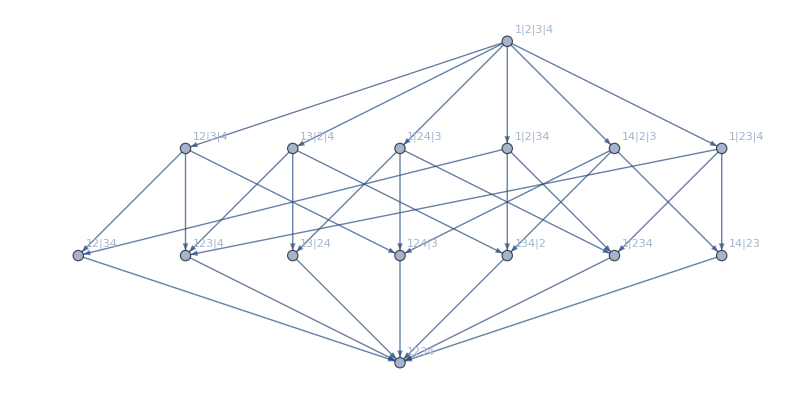
-Graphics-1 | -Graphics-363
-Graphics-
-Graphics--n1x2x34+n1x2x3x4x^4-x^3
(x-1) x^3
 *  * 0854192
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood4[1]
```